```mathematica
x={3.333333333,2.111111111,3.333333333,3.333333333,2.222222222,4.555555556,3.222222222,4.888888889}
y={1.492870563,2.282432067,1.874211504,1.653012681,1.86160245,3.561856737,3.826609938,4.57712854}
z={0.123217641,0.320608017,0.218552876,0.16325317,0.215400613,0.640464184,0.706652485,0.894282135}
```

{3.33333,2.11111,3.33333,3.33333,2.22222,4.55556,3.22222,4.88889}

{1.49287,2.28243,1.87421,1.65301,1.8616,3.56186,3.82661,4.57713}

{0.123218,0.320608,0.218553,0.163253,0.215401,0.640464,0.706652,0.894282}

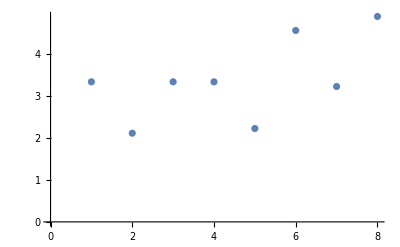

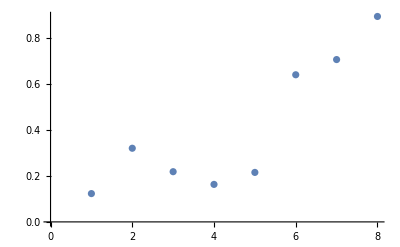

```mathematica
ListPlot[x]
ListPlot[z]
```

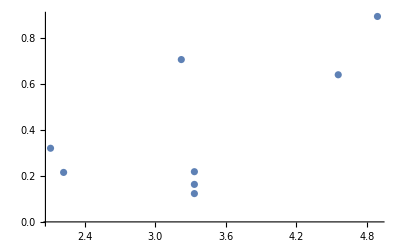

```mathematica
ListPlot[Transpose[{x,z}]]
```

```mathematica
PearsonCorrelationTest[x,z,"TestDataTable"]
```

| Statistic | P-Value
Pearson Correlation | 0.66431 | 0.0723593

```mathematica
SpearmanRankTest[x,z,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | 0.268373 | 0.520441

```mathematica
IndependenceTest[x,z,"TestDataTable"]
ListPlot[Transpose[{x,z}]]
```

| Statistic | P-Value
Pearson Correlation | 0.66431 | 0.0723593

-Graphics-

```mathematica
csv=Import[NotebookDirectory[] <> "saliency.csv", "table", FieldSeparators -> ";"]
```

{{Xinhan Di,Sean Bruton,Xinhan Di,Lu,Atul,Fan Li,Xinwei Xiong,Ziggy,Jackey},{trial 1,1,4,3,2,5,5,4,3,3},{trial 2,1,1,3,1,4,5,2,1,1},{trial 3,2,3,4,2,4,4,3,5,3},{trial 4,3,4,5,3,3,3,3,2,4},{trial 5,2,4,2,2,2,3,1,1,3},{trial 6,3,5,5,4,5,5,5,5,4},{trial 7,4,4,3,2,2,2,3,4,5},{trial 8,4,5,5,5,5,5,5,5,5}}

```mathematica
s=csv[[2]][[1;;]]
```

{trial 1,1,4,3,2,5,5,4,3,3}

```mathematica
csv=Import[NotebookDirectory[] <> "saliency.csv", "table", FieldSeparators -> ";"]
```

{{Xinhan Di,Sean Bruton,Xinhan Di,Lu,Atul,Fan Li,Xinwei Xiong,Ziggy,Jackey},{trial 1,1,4,3,2,5,5,4,3,3},{trial 2,1,1,3,1,4,5,2,1,1},{trial 3,2,3,4,2,4,4,3,5,3},{trial 4,3,4,5,3,3,3,3,2,4},{trial 5,2,4,2,2,2,3,1,1,3},{trial 6,3,5,5,4,5,5,5,5,4},{trial 7,4,4,3,2,2,2,3,4,5},{trial 8,4,5,5,5,5,5,5,5,5}}

```mathematica
s=csv[[2]][[2;;]]
```

{1,4,3,2,5,5,4,3,3}

```mathematica
list=Table[{#,z[[i-1]]}&/@csv[[i]][[2;;]],{i,2,Length[csv]}]
```

{{{1,0.123218},{4,0.123218},{3,0.123218},{2,0.123218},{5,0.123218},{5,0.123218},{4,0.123218},{3,0.123218},{3,0.123218}},{{1,0.320608},{1,0.320608},{3,0.320608},{1,0.320608},{4,0.320608},{5,0.320608},{2,0.320608},{1,0.320608},{1,0.320608}},{{2,0.218553},{3,0.218553},{4,0.218553},{2,0.218553},{4,0.218553},{4,0.218553},{3,0.218553},{5,0.218553},{3,0.218553}},{{3,0.163253},{4,0.163253},{5,0.163253},{3,0.163253},{3,0.163253},{3,0.163253},{3,0.163253},{2,0.163253},{4,0.163253}},{{2,0.215401},{4,0.215401},{2,0.215401},{2,0.215401},{2,0.215401},{3,0.215401},{1,0.215401},{1,0.215401},{3,0.215401}},{{3,0.640464},{5,0.640464},{5,0.640464},{4,0.640464},{5,0.640464},{5,0.640464},{5,0.640464},{5,0.640464},{4,0.640464}},{{4,0.706652},{4,0.706652},{3,0.706652},{2,0.706652},{2,0.706652},{2,0.706652},{3,0.706652},{4,0.706652},{5,0.706652}},{{4,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282}}}

```mathematica
Flatten[list,1]
```

{{1,0.123218},{4,0.123218},{3,0.123218},{2,0.123218},{5,0.123218},{5,0.123218},{4,0.123218},{3,0.123218},{3,0.123218},{1,0.320608},{1,0.320608},{3,0.320608},{1,0.320608},{4,0.320608},{5,0.320608},{2,0.320608},{1,0.320608},{1,0.320608},{2,0.218553},{3,0.218553},{4,0.218553},{2,0.218553},{4,0.218553},{4,0.218553},{3,0.218553},{5,0.218553},{3,0.218553},{3,0.163253},{4,0.163253},{5,0.163253},{3,0.163253},{3,0.163253},{3,0.163253},{3,0.163253},{2,0.163253},{4,0.163253},{2,0.215401},{4,0.215401},{2,0.215401},{2,0.215401},{2,0.215401},{3,0.215401},{1,0.215401},{1,0.215401},{3,0.215401},{3,0.640464},{5,0.640464},{5,0.640464},{4,0.640464},{5,0.640464},{5,0.640464},{5,0.640464},{5,0.640464},{4,0.640464},{4,0.706652},{4,0.706652},{3,0.706652},{2,0.706652},{2,0.706652},{2,0.706652},{3,0.706652},{4,0.706652},{5,0.706652},{4,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282},{5,0.894282}}

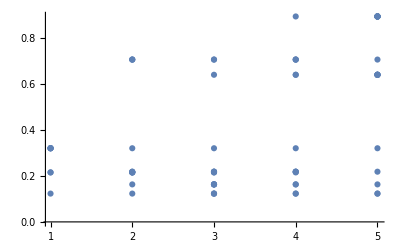

```mathematica
ListPlot[Flatten[list,1]]
```